## Pulsar analysis

```mathematica
Get@"init.m"
""
""
(*These first Four won't work (everywhere?) for some reason, but I can use traditional form anyway. *)
(*Notation[∂f_[x_]/∂x_ ⟸ D[f_,x_]]
Notation[∂^n_ f_[x_]/∂x_^n_ ⟸ D[f_,{x_,n_}]]

Notation[ⅆf_[x_]/ⅆx_ ⟸ Dt[f_][x_]]
Notation[ⅆ^n_ f_[x_]/ⅆ x_^n_ ⟸ Dt[f_][{x_,n_}]]*)

Notation[(∂f_/∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_/∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[(∂/∂x_)f_  ⟹ D[f_,x_]]
Notation[(∂^n_ /∂x_^n_)f_  ⟹ D[f_,{x_,n_}]]
Notation[∂f_/∂x_  ⟹ D[f_,x_]]
Notation[∂^n_ f_/∂x_^n_  ⟹ D[f_,{x_,n_}]]
Notation[∂/∂x_(f_)  ⟹ D[f_,x_]]
Notation[∂^n_ /∂x_^n_(f_)  ⟹ D[f_,{x_,n_}]]

Notation[(ⅆf_/ⅆx_)  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_ f_/ⅆ x_^n_)  ⟹ Dt[f_,{x_,n_}]]
Notation[(ⅆ/ⅆx_)f_  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_/ⅆ x_^n_)f_  ⟹ Dt[f_,{x_,n_}]]


Notation[(∂f_/∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_/∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[(∂/∂x_)f_  ⟹ D[f_,x_]]
Notation[(∂^n_ /∂x_^n_)f_  ⟹ D[f_,{x_,n_}]]
Notation[∂f_/∂x_  ⟹ D[f_,x_]]
Notation[∂^n_ f_/∂x_^n_  ⟹ D[f_,{x_,n_}]]
Notation[∂/∂x_(f_)  ⟹ D[f_,x_]]
Notation[∂^n_ /∂x_^n_(f_)  ⟹ D[f_,{x_,n_}]]

Notation[(ⅆf_/ⅆx_)  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_ f_/ⅆ x_^n_)  ⟹ Dt[f_,{x_,n_}]]
Notation[(ⅆ/ⅆx_)f_  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_/ⅆ x_^n_)f_  ⟹ Dt[f_,{x_,n_}]]
"Notations"
"Notations"
Notation[∂/(∂x_) f_  ⟹ D[f_,x_]]
Notation[(∂f_)/(∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_)/(∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[∂^n_/(∂x_^n_) f_ ⟹ D[f_,{x_,n_}]]

(* Mixed partials *)
Notation[(∂^2 f_)/(∂x_∂y_) ⟹ D[f_,x_,y_]]

Notation[∂^2/(∂x_∂y_)f_ ⟹ D[f_,x_,y_]]
(* Next two currently don't work *)
(*Notation[(∂^(n_+m_) f_)/(∂x_^n_∂y_^m_) ⟹ D[f_,{x_,n_},{y_,m_}]]
Notation[∂^(n_+m_)/(∂x_^n_∂y_^m_) f_ ⟹ D[f_,{x_,n_},{y_,m_}]]*)
"Fixed notation"
"Fixed notation"
SetOptions[Plot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ContourPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[ParametricPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ReImPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[VectorPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[DensityPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[ComplexPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[Plot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2},PlotLabels->Automatic,PlotRange->All];
SetOptions[ListPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[ContourPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[VectorPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[SliceVectorPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[DensityPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[ComplexPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2},PlotRange->All];
"plotting options"
"plotting options"
SetOptions[Manipulate,Paneled->False];
"more options"
"more options"
```

Notations

Notations

Fixed notation

Fixed notation

plotting options

plotting options

more options

more options

WolframAlphaQueryParseResults

-Graphics-

```mathematica
1/ 1. 3373
```

0.747775

```mathematica
10^51
```

1000000000000000000000000000000000000000000000000000

WolframAlphaQueryParseResults

Tue 11 Jan 2022

```mathematica
TeXForm[-11/(-3(x^2)^(1/10))]
```

\frac{11}{3 \sqrt[10]{x^2}}

```mathematica
D[(1/f), f]
```

-1/f^2

```mathematica
p=1/f
```

1/f

```mathematica
Δf=10^-3
```

1/1000

```mathematica
ClearAll@Δf
```

```mathematica
Δp=√((D[(1/f), f] Δf)^2)
%//PowerExpand
```

√(Δf^2/f^4)

Δf/f^2

```mathematica
μ=2
```

2

```mathematica
σ=√(1/M((1-μ)^2+(3-μ)^2))/.M->2
```

1

```mathematica
σ/μ^2
```

1/4

```mathematica
6.8 * 10 - 7.662 * 10^-3
```

67.9923

```mathematica
6.8 10^1-7+1.662 10^-3
```

61.0017

### Calculations on the quantities

```mathematica
c=LinguisticAssistant;
p0=wa["76 * 10^-7 +1.662*10^-3 seconds"]
p0::usage="This is the period at the equilibrium line of the sine wave.";
p=wa["83*10^-7 + 1.662*10^-3 seconds"]
p::usage="This is the period of the sine wave at the highest amplitude";
```

0.0016696 s

0.0016703 s

```mathematica
vs=c(p0/p-1)//UnitConvert[#,"Kilometers"/"Seconds"]&
```

-125.639 km/s

According to the verified formula further below.

```mathematica
vsAlt=(c(p-p0))/p0//UnitConvert[#,"Kilometers"/"Seconds"]&
```

125.692 km/s

```mathematica
T=wa["0.16+5.63 10^4 days"]
T::usage="The period corresponding to the orbit of the pulsar around the center of mass. It is calculated using the period of the sine wave.";
```

56.94 days

```mathematica
r=(Abs@vs T)/(2π)
```

9.83729×10^7 km

```mathematica
r/LinguisticAssistant
```

247.432

```mathematica
T^2/r^3==(4 π^2)/(G(MP+MC))//Solve[#,MC]&
```

{{MC→(-G T^2 MP+4 r^3 π^2)/(G T^2)}}

```mathematica
G=LinguisticAssistant//UnitConvert
Mp=LinguisticAssistant;
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Mc=(-G T^2 Mp+4 r^3 π^2)/(G T^2)
```

2.02832×10^31 kg

```mathematica
Mc/LinguisticAssistant
```

10.2006

if the mass of the companion is sufficiently big, we approximate F = F_c, then

```mathematica
v=Abs@vs
```

125.639 km/s

```mathematica
Mc=(v^2 r)/G
```

2.32658×10^31 kg

```mathematica
Mc/LinguisticAssistant
```

11.7006

Verifying the modified julian date

```mathematica
LinguisticAssistant
```

Year: 2012

```mathematica
v/LinguisticAssistant
```

-4.21853

```mathematica
v/LinguisticAssistant
```

-2.65274

#### More quantities

```mathematica
ρ==M/(4/3 π R^3)//Solve[#,R]&
```

{{R→-(M^(1/3) (-3/π)^(1/3))/(2^(2/3) ρ^(1/3))},{R→(M^(1/3) (3/π)^(1/3))/(2^(2/3) ρ^(1/3))},{R→((-1)^(2/3) M^(1/3) (3/π)^(1/3))/(2^(2/3) ρ^(1/3))}}

Assume the density of the sun

```mathematica
R=R/.%[[2]][[1]]/.{M->Mc,ρ->LinguisticAssistant}//UnitConvert
```

1.58007×10^9 m

```mathematica
R/LinguisticAssistant
```

2.27119

```mathematica
R/LinguisticAssistant
```

3.97433

#### Verifying Doppler

-Graphics-

```mathematica
p==p0(1+v/c)//Solve[#,v]&
```

{{v→(c (p-p0))/p0}}

#### Mass function

It gives a lower bound for the mass of the companion star.

-Graphics-

```mathematica
i=90°;
McMinimal=T/(2π G)K1^3/.K1->v Sin[i]
```

2.32658×10^31 kg

```mathematica
McMinimal/Mc
```

1.

```mathematica
McMinimal/Mp
```

7.80052

```mathematica
LinguisticAssistant/LinguisticAssistant
```

333000.

The ratio of the companion star to the pulsar is much smaller than the ratio of the sun to the earth; is it reasonable to assume that the pulsar orbits around the companion (situation 2)?

#### Conservation of angular momentum

Can we use conservation of angular momentum to determine r_1 and r_2?

ℓ = | r×p | = r m v sin θ

#### Try to fit in MMA

```mathematica
x ={56300.4688155539,56300.45492639893,56300.44103724313,56300.42714808649,56300.413258929024,56300.39936977075,56300.38548061164,56300.37159145176,56300.35770229113,56300.34381312978};
y = {0.0016627957592090326,0.00166282563896264,0.0016628302415629193,0.0016628131097909669,0.0016627781654799023,0.0016627323139534107,0.0016626925155149316,0.0016626750457100386,0.0016626881480292916,0.001662710837899844};
```

```mathematica
ClearAll[x]
```

```mathematica
FindFit[y ,B+A Sin[ω x + ϕ],{B, A, ω, ϕ},x]
```

{B→0.00166275,A→-7.81285×10^-8,ω→0.574299,ϕ→3.12734}

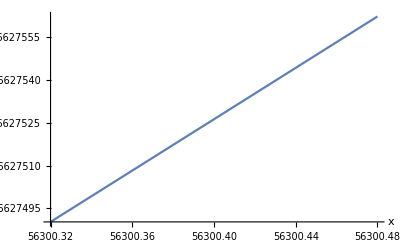

```mathematica
Plot[B+A Sin[ω x + ϕ]/.{B->0.0016627541982398835,A->-7.812853029524281*^-8,ω->0.5742990387992161,ϕ->3.127343164656341},{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
```

```mathematica
ω==2π f//Solve[#,f]&
```

{{f→ω/(2 π)}}

```mathematica
0.5742990387992161/(2π)
```

0.0914025

```mathematica
1/0.16
```

6.25